```mathematica
CIRCLE1X=-0.70
```

-0.7

```mathematica
CIRCLE1X
```

-0.7

```mathematica
CIRCLE1Y=2.20
```

2.2

```mathematica
topTip = 
  {{Sqrt[{-CIRCLE1X + x + 0.5} - {-CIRCLE1X + x + 0.5}^
         {2}]} + CIRCLE1Y}*((1-i)*UnitStep[-CIRCLE1X + x + 0.39]+i)
```

{{{(2.2+√(1.2+x-(1.2+x)^2)) (i+(1-i) UnitStep[1.09+x])}}}

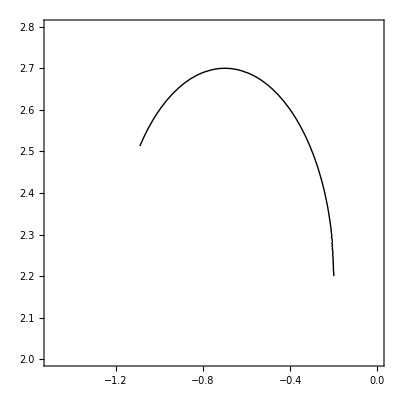

```mathematica
topTipGraph = ContourPlot[{topTip-y==0}, {x, -1.5, 0}, {y, 2, 2.8}, 
   ContourStyle -> {Thick,Black}]
```

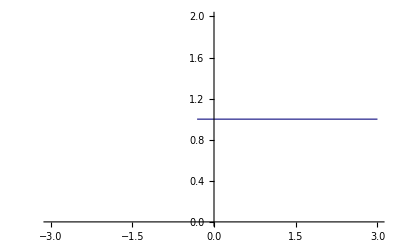

```mathematica
Plot[((1-i)*UnitStep[-CIRCLE1X + x -0.39]+i),{x,-3,3}]
```

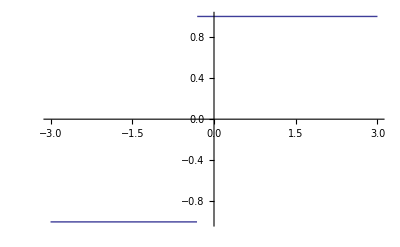

```mathematica
Plot[Sign[-CIRCLE1X + x -0.39],{x,-3,3}]
```

```mathematica
leftTip=({CIRCLE1Y-Sqrt[({x-CIRCLE1X+0.5})-({x-CIRCLE1X+0.5})^{2}]})*((1-i)*UnitStep[-CIRCLE1X + x -0.39]+i)
```

{{(2.2-√(1.2+x-(1.2+x)^2)) (i+(1-i) UnitStep[0.31+x])}}

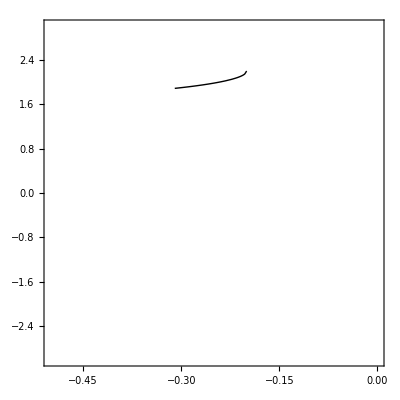

```mathematica
leftTipGraph = ContourPlot[{leftTip==y}, {x, -0.5, 0}, {y, -3, 3}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
CIRCLE2X=0.55
```

0.55

```mathematica
CIRCLE2Y=-0.37
```

-0.37

```mathematica
rightTipTop = ({CIRCLE2Y+({Sqrt[({x-CIRCLE2X+0.5})-({x-CIRCLE2X+0.5})^{2}]})})*((1-i)*UnitStep[x-CIRCLE2X+0.424]+i)
```

{{{(-0.37+√(-0.05-(-0.05+x)^2+x)) (i+(1-i) UnitStep[-0.126+x])}}}

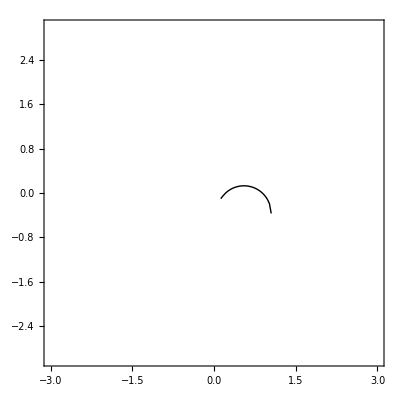

```mathematica
rightTipTopGraph = ContourPlot[{rightTipTop==y}, {x, -3, 3}, {y, -3, 3}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
rightTipRight = ({CIRCLE2Y-Sqrt[({x-CIRCLE2X+0.5})-({x-CIRCLE2X+0.5})^{2}]})*((1-i)*UnitStep[x-CIRCLE2X-0.39]+i)
```

{{(-0.37-√(-0.05-(-0.05+x)^2+x)) (i+(1-i) UnitStep[-0.94+x])}}

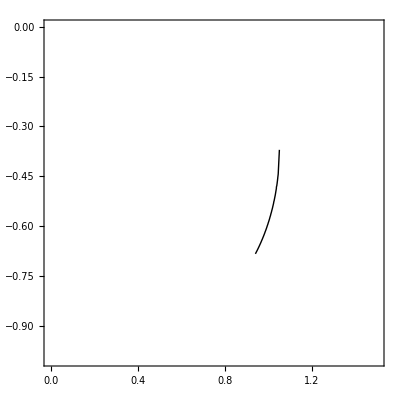

```mathematica
rightTipRightGraph = ContourPlot[{rightTipRight==y}, {x, 0, 1.5}, {y, -1, 0}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
CIRCLE3SCALE=3.71
```

3.71

```mathematica
CIRCLE3AND4Y=0.37
```

0.37

```mathematica
CIRCLE3AND4X=-0.62
```

-0.62

```mathematica
bigCircleBottom =({CIRCLE3AND4Y-CIRCLE3SCALE*({Sqrt[({{{x-CIRCLE3AND4X}/{CIRCLE3SCALE}}+0.5})-({{{x-CIRCLE3AND4X}/{CIRCLE3SCALE}}+0.5})^{2}]})})*((1-i)*UnitStep[{{-{x-CIRCLE3AND4X}/{CIRCLE3SCALE}}+0.324}]+i)
```

{{{{{(0.37-3.71 √(0.5+0.269542 (0.62+x)-(0.5+0.269542 (0.62+x))^2)) (i+(1-i) UnitStep[0.324+0.269542 (-0.62-x)])}}}}}

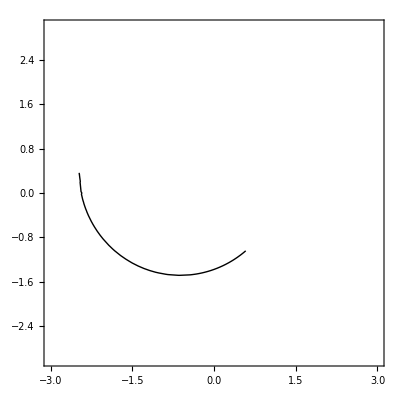

```mathematica
bigCircleBottomGraph = ContourPlot[{bigCircleBottom==y}, {x, -3, 3}, {y, -3, 3}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
bigCircleTop =({CIRCLE3AND4Y+CIRCLE3SCALE*Sqrt[({{{x-CIRCLE3AND4X}/{CIRCLE3SCALE}}+0.5})-({{{x-CIRCLE3AND4X}/{CIRCLE3SCALE}}+0.5})^{2}]})*((1-i)*UnitStep[{-{{x-CIRCLE3AND4X}/{CIRCLE3SCALE}}-0.388}]+i)
```

{{{{(0.37+3.71 √(0.5+0.269542 (0.62+x)-(0.5+0.269542 (0.62+x))^2)) (i+(1-i) UnitStep[-0.388-0.269542 (0.62+x)])}}}}

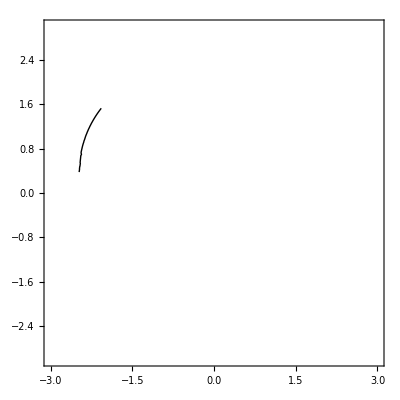

```mathematica
bigCircleTopGraph = ContourPlot[{bigCircleTop==y}, {x, -3, 3}, {y, -3, 3}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
({CIRCLE3AND4Y-CIRCLE4SCALE *({Sqrt[({{{x-CIRCLE3AND4X}/{CIRCLE4SCALE}}+0.5})-({{{x-CIRCLE3AND4X}/{CIRCLE4SCALE}}+0.5})^{2}]})}) * 0.5 *({1+Sign[{-{{x-CIRCLE3AND4X}/{CIRCLE4SCALE}}+0.324}]})
```

{{{{{0.5 (0.37-1.72 √(0.5+0.581395 (0.62+x)-(0.5+0.581395 (0.62+x))^2)) (1+Sign[0.324-0.581395 (0.62+x)])}}}}}

```mathematica
CIRCLE4SCALE=1.72
```

1.72

```mathematica
smallCircleBottom = ({CIRCLE3AND4Y-CIRCLE4SCALE *({Sqrt[({{{x-CIRCLE3AND4X}/{CIRCLE4SCALE}}+0.5})-({{{x-CIRCLE3AND4X}/{CIRCLE4SCALE}}+0.5})^{2}]})}) *((1-i)*UnitStep[{-{{x-CIRCLE3AND4X}/{CIRCLE4SCALE}}+0.324}]+i)
```

{{{{{(0.37-1.72 √(0.5+0.581395 (0.62+x)-(0.5+0.581395 (0.62+x))^2)) (i+(1-i) UnitStep[0.324-0.581395 (0.62+x)])}}}}}

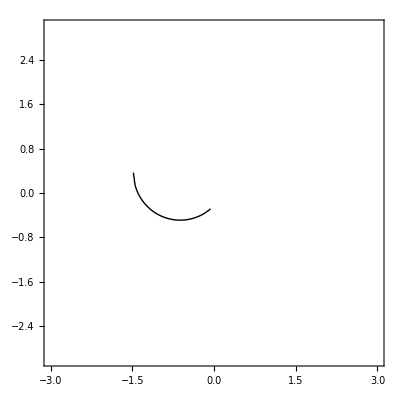

```mathematica
smallCircleBottomGraph = ContourPlot[{smallCircleBottom==y}, {x, -3, 3}, {y, -3, 3}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
smallCircleTop =({CIRCLE3AND4Y+CIRCLE4SCALE * Sqrt[({{{x-CIRCLE3AND4X}/{CIRCLE4SCALE}}+0.5})-({{{x-CIRCLE3AND4X}/{CIRCLE4SCALE}}+0.5})^{2}]}) *((1-i)*UnitStep[{-{{x-CIRCLE3AND4X}/{CIRCLE4SCALE}}-0.39}]+i)
```

{{{{(0.37+1.72 √(0.5+0.581395 (0.62+x)-(0.5+0.581395 (0.62+x))^2)) (i+(1-i) UnitStep[-0.39-0.581395 (0.62+x)])}}}}

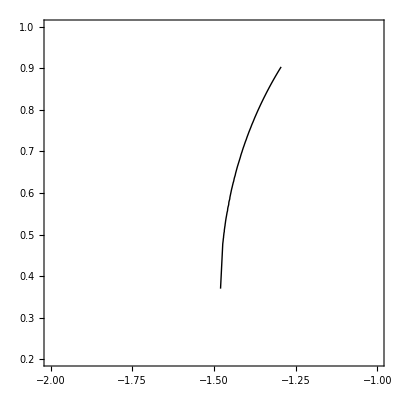

```mathematica
smallCircleTopGraph = ContourPlot[{smallCircleTop==y}, {x, -2, -1}, {y, 0.2, 1}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
Plot3D[{ (topTip-y)*(leftTip-y)*(rightTipTop-y)*(rightTipRight-y)*( bigCircleTop-y)*( bigCircleBottom-y)*( smallCircleTop-y)*(smallCircleBottom-y)}, {x, -3, 3}, {y, -3, 3},Mesh->None,Axes->False,MaxRecursion->15]
```

-Graphics3D-

```mathematica
LINE1Y=1.55
```

1.55

```mathematica
LINE1WIDTH=0.97
```

0.97

```mathematica
LINE1X=-2.054
```

-2.054

```mathematica
line1 = ((1-i)*UnitStep[-LINE1X + x ]+i)*({x-LINE1X+LINE1Y})*((1-i)*UnitStep[+LINE1X +LINE1WIDTH - x ]+i)
```

{(3.604+x) (i+(1-i) UnitStep[-1.084-x]) (i+(1-i) UnitStep[2.054+x])}

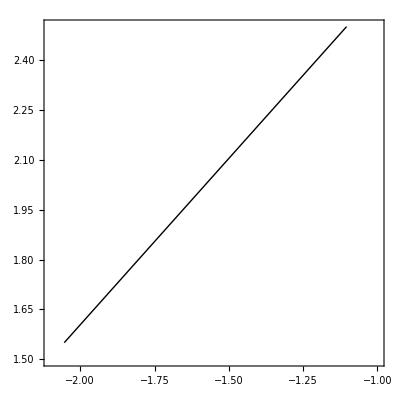

```mathematica
line1Graph = ContourPlot[{line1==y}, {x, -2.1, -1}, {y, 1.5, 2.5}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
LINE2Y=0.9
```

0.9

```mathematica
LINE2WIDTH=1
```

1

```mathematica
LINE2X=-1.3
```

-1.3

```mathematica
line2=((1-i)*UnitStep[-LINE2X + x ]+i)*({x-LINE2X+LINE2Y})*((1-i)*UnitStep[+LINE2X +LINE2WIDTH - x ]+i)
```

{(2.2+x) (i+(1-i) UnitStep[-0.3-x]) (i+(1-i) UnitStep[1.3+x])}

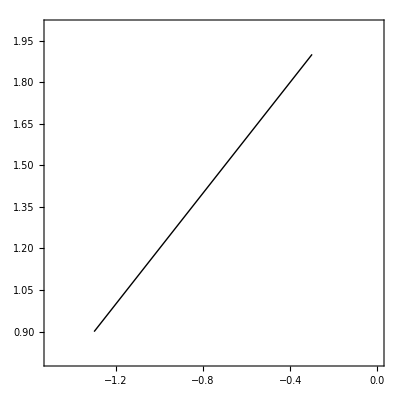

```mathematica
line2Graph = ContourPlot[{line2==y}, {x, -1.5, 0}, {y, 0.8, 2}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
LINE3Y=-0.28
```

-0.28

```mathematica
LINE3WIDTH=0.3
```

0.3

```mathematica
LINE3X=-0.059
```

-0.059

```mathematica
line3 = ((1-i)*UnitStep[-LINE3X + x ]+i)*({x-LINE3X+LINE3Y})*((1-i)*UnitStep[+LINE3X +LINE3WIDTH - x ]+i)
```

{(-0.221+x) (i+(1-i) UnitStep[0.241-x]) (i+(1-i) UnitStep[0.059+x])}

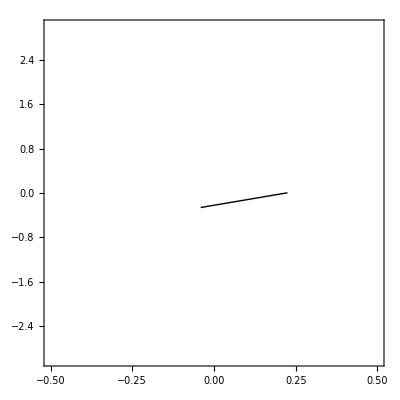

```mathematica
line3Graph = ContourPlot[{line3==y}, {x, -0.5, 0.5}, {y, -3, 3}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
LINE4Y=-1.045
```

-1.045

```mathematica
LINE4WIDTH=0.355
```

0.355

```mathematica
LINE4X=0.58
```

0.58

```mathematica
line4 = ((1-i)*UnitStep[-LINE4X + x ]+i)*({x-LINE4X+LINE4Y})*((1-i)*UnitStep[+LINE4X +LINE4WIDTH - x ]+i)
```

{(-1.625+x) (i+(1-i) UnitStep[0.935-x]) (i+(1-i) UnitStep[-0.58+x])}

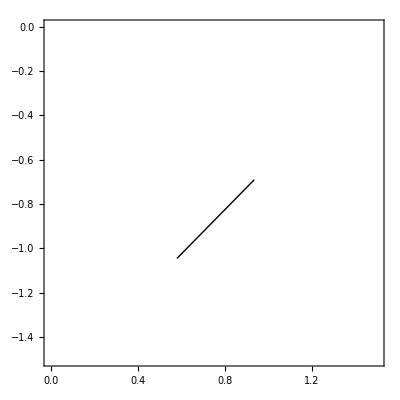

```mathematica
line4Graph = ContourPlot[{line4==y}, {x, 0, 1.5}, {y, -1.5, 0}, 
  ContourStyle -> {Thick,Black}]
```

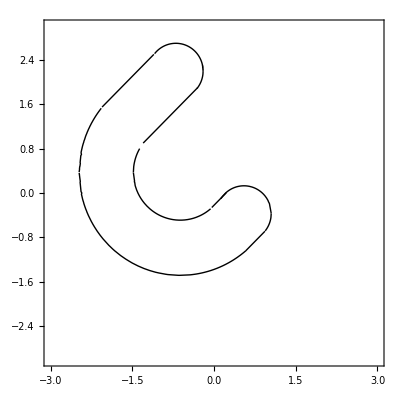

```mathematica
Show[topTipGraph,leftTipGraph,rightTipTopGraph, rightTipRightGraph, bigCircleTopGraph,  bigCircleBottomGraph, smallCircleTopGraph, smallCircleBottomGraph,line1Graph,line2Graph,line3Graph,line4Graph, PlotRange -> {{-3,3},{-3,3}}]
```

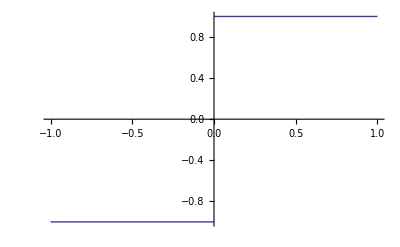

```mathematica
Plot[Sign[x],{x,-1,1}]
```

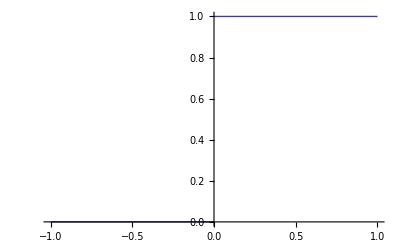

```mathematica
Plot[UnitStep[x],{x,-1,1}]
```

```mathematica
ALL INVERTED
```

ALL INVERTED

```mathematica
topTipInv = 
  {{Sqrt[{-CIRCLE1X - x + 0.5} - {-CIRCLE1X - x + 0.5}^
         {2}]} + CIRCLE1Y}*((1-i)*UnitStep[-CIRCLE1X - x + 0.39]+i)
```

{{{(2.2+√(1.2-(1.2-x)^2-x)) (i+(1-i) UnitStep[1.09-x])}}}

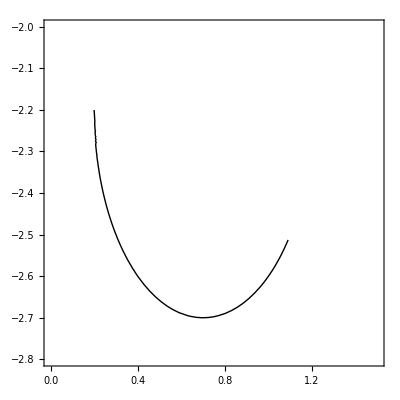

```mathematica
topTipGraphInv = ContourPlot[{-topTipInv==y}, {x,  0,1.5}, {y, -2.8, -2}, 
   ContourStyle -> {Thick,Black}]
```

```mathematica
leftTipInv=({CIRCLE1Y-Sqrt[({-x-CIRCLE1X+0.5})-({-x-CIRCLE1X+0.5})^{2}]})*((1-i)*UnitStep[-CIRCLE1X - x -0.39]+i)
```

{{(2.2-√(1.2-(1.2-x)^2-x)) (i+(1-i) UnitStep[0.31-x])}}

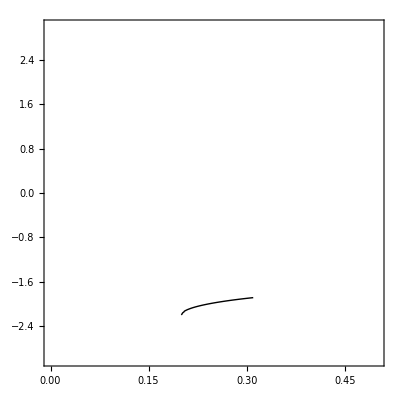

```mathematica
leftTipGraphInv = ContourPlot[{leftTipInv==-y}, {x, 0, 0.5}, {y, -3, 3}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
rightTipTopInv = ({CIRCLE2Y+({Sqrt[({-x-CIRCLE2X+0.5})-({-x-CIRCLE2X+0.5})^{2}]})})*((1-i)*UnitStep[-x-CIRCLE2X+0.424]+i)
```

{{{(-0.37+√(-0.05-(-0.05-x)^2-x)) (i+(1-i) UnitStep[-0.126-x])}}}

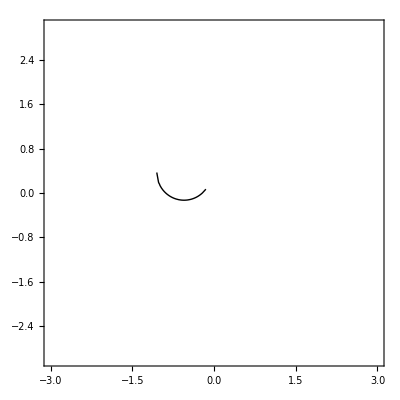

```mathematica
rightTipTopGraphInv = ContourPlot[{rightTipTopInv==-y}, {x, -3, 3}, {y, -3, 3}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
rightTipRightInv = ({CIRCLE2Y-Sqrt[({-x-CIRCLE2X+0.5})-({-x-CIRCLE2X+0.5})^{2}]})*((1-i)*UnitStep[-x-CIRCLE2X-0.39]+i)
```

{{(-0.37-√(-0.05-(-0.05-x)^2-x)) (i+(1-i) UnitStep[-0.94-x])}}

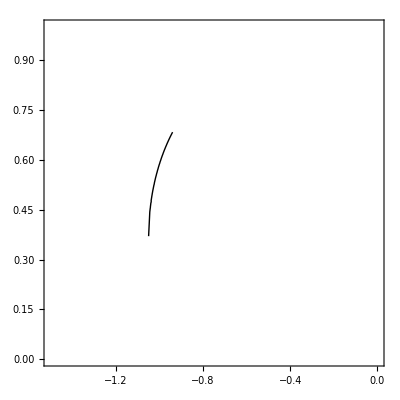

```mathematica
rightTipRightGraphInv = ContourPlot[{rightTipRightInv==-y}, {x, -1.5, 0}, {y, 0, 1}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
bigCircleBottomInv =({CIRCLE3AND4Y-CIRCLE3SCALE*({Sqrt[({{{-x-CIRCLE3AND4X}/{CIRCLE3SCALE}}+0.5})-({{{-x-CIRCLE3AND4X}/{CIRCLE3SCALE}}+0.5})^{2}]})})*((1-i)*UnitStep[{{-{-x-CIRCLE3AND4X}/{CIRCLE3SCALE}}+0.324}]+i)
```

{{{{{(0.37-3.71 √(0.5-(0.5+0.269542 (0.62-x))^2+0.269542 (0.62-x))) (i+(1-i) UnitStep[0.324+0.269542 (-0.62+x)])}}}}}

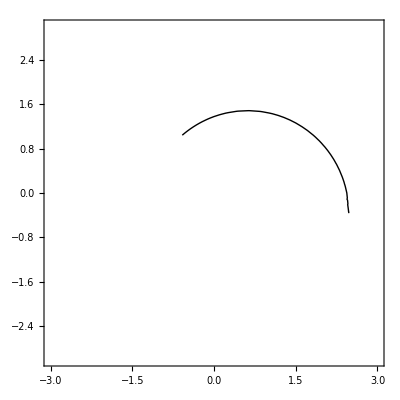

```mathematica
bigCircleBottomGraphInv = ContourPlot[{bigCircleBottomInv==-y}, {x, -3, 3}, {y, -3, 3}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
bigCircleTopInv =({CIRCLE3AND4Y+CIRCLE3SCALE*Sqrt[({{{-x-CIRCLE3AND4X}/{CIRCLE3SCALE}}+0.5})-({{{-x-CIRCLE3AND4X}/{CIRCLE3SCALE}}+0.5})^{2}]})*((1-i)*UnitStep[{-{{-x-CIRCLE3AND4X}/{CIRCLE3SCALE}}-0.388}]+i)
```

{{{{(0.37+3.71 √(0.5-(0.5+0.269542 (0.62-x))^2+0.269542 (0.62-x))) (i+(1-i) UnitStep[-0.388-0.269542 (0.62-x)])}}}}

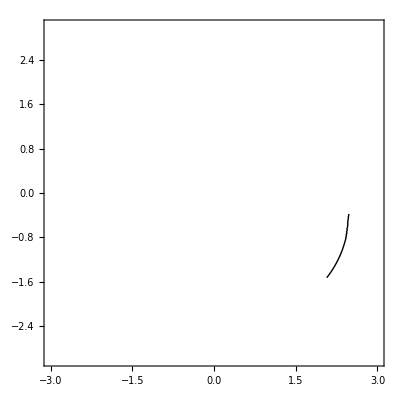

```mathematica
bigCircleTopGraphInv = ContourPlot[{bigCircleTopInv==-y}, {x, -3, 3}, {y, -3, 3}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
smallCircleBottomInv = ({CIRCLE3AND4Y-CIRCLE4SCALE *({Sqrt[({{{-x-CIRCLE3AND4X}/{CIRCLE4SCALE}}+0.5})-({{{-x-CIRCLE3AND4X}/{CIRCLE4SCALE}}+0.5})^{2}]})}) *((1-i)*UnitStep[{-{{-x-CIRCLE3AND4X}/{CIRCLE4SCALE}}+0.324}]+i)
```

{{{{{(0.37-1.72 √(0.5-(0.5+0.581395 (0.62-x))^2+0.581395 (0.62-x))) (i+(1-i) UnitStep[0.324-0.581395 (0.62-x)])}}}}}

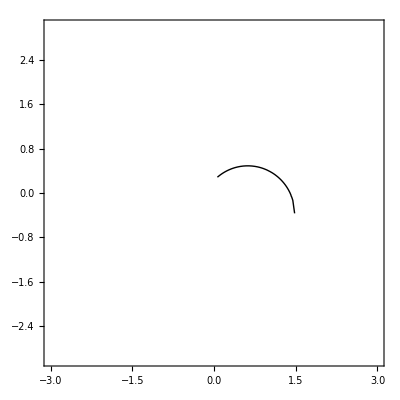

```mathematica
smallCircleBottomGraphInv = ContourPlot[{smallCircleBottomInv==-y}, {x, -3, 3}, {y, -3, 3}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
smallCircleTopInv =({CIRCLE3AND4Y+CIRCLE4SCALE * Sqrt[({{{-x-CIRCLE3AND4X}/{CIRCLE4SCALE}}+0.5})-({{{-x-CIRCLE3AND4X}/{CIRCLE4SCALE}}+0.5})^{2}]}) *((1-i)*UnitStep[{-{{-x-CIRCLE3AND4X}/{CIRCLE4SCALE}}-0.39}]+i)
```

{{{{(0.37+1.72 √(0.5-(0.5+0.581395 (0.62-x))^2+0.581395 (0.62-x))) (i+(1-i) UnitStep[-0.39-0.581395 (0.62-x)])}}}}

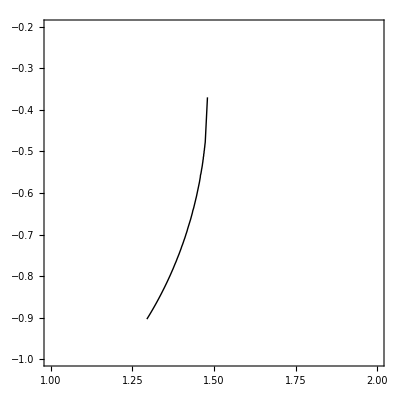

```mathematica
smallCircleTopGraphInv = ContourPlot[{smallCircleTopInv==-y}, {x, 1, 2}, {y, -1, -0.2}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
line1Inv = ((1-i)*UnitStep[-LINE1X - x ]+i)*({-x-LINE1X+LINE1Y})*((1-i)*UnitStep[+LINE1X +LINE1WIDTH + x ]+i)
```

{(3.604-x) (i+(1-i) UnitStep[2.054-x]) (i+(1-i) UnitStep[-1.084+x])}

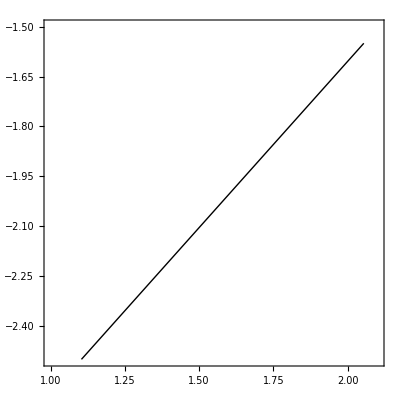

```mathematica
line1GraphInv = ContourPlot[{line1Inv==-y}, {x, 1, 2.1}, {y, -2.5, -1.5}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
line2Inv=((1-i)*UnitStep[-LINE2X - x ]+i)*({-x-LINE2X+LINE2Y})*((1-i)*UnitStep[+LINE2X +LINE2WIDTH + x ]+i)
```

{(2.2-x) (i+(1-i) UnitStep[1.3-x]) (i+(1-i) UnitStep[-0.3+x])}

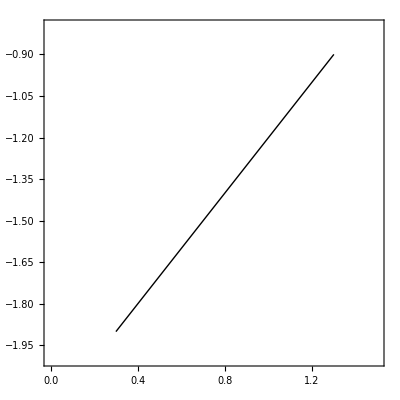

```mathematica
line2GraphInv = ContourPlot[{line2Inv==-y}, {x, 0, 1.5}, {y, -2, -0.8}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
line3Inv = ((1-i)*UnitStep[-LINE3X - x ]+i)*({-x-LINE3X+LINE3Y})*((1-i)*UnitStep[+LINE3X +LINE3WIDTH + x ]+i)
```

{(-0.221-x) (i+(1-i) UnitStep[0.059-x]) (i+(1-i) UnitStep[0.241+x])}

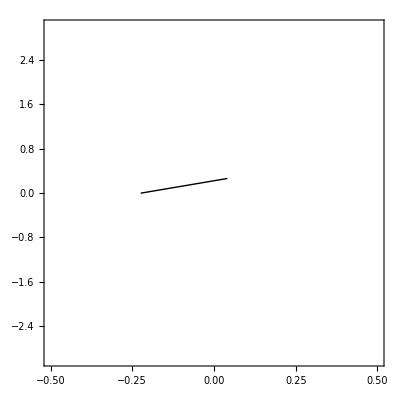

```mathematica
line3GraphInv = ContourPlot[{line3Inv==-y}, {x, -0.5, 0.5}, {y, -3, 3}, 
  ContourStyle -> {Thick,Black}]
```

```mathematica
line4Inv = ((1-i)*UnitStep[-LINE4X - x ]+i)*({-x-LINE4X+LINE4Y})*((1-i)*UnitStep[+LINE4X +LINE4WIDTH + x ]+i)
```

{(-1.625-x) (i+(1-i) UnitStep[-0.58-x]) (i+(1-i) UnitStep[0.935+x])}

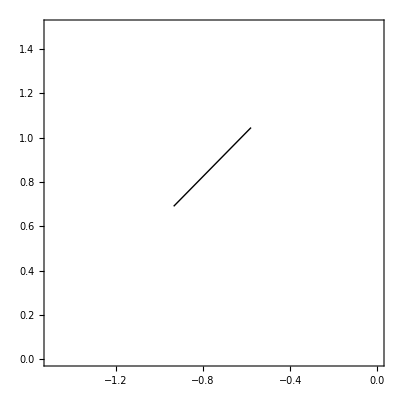

```mathematica
line4GraphInv = ContourPlot[{line4Inv==-y}, {x, -1.5, 0}, {y, 0, 1.5}, 
  ContourStyle -> {Thick,Black}]
```

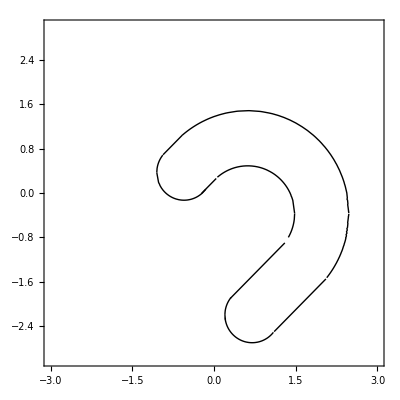

```mathematica
Show[topTipGraphInv,leftTipGraphInv,rightTipTopGraphInv, rightTipRightGraphInv, bigCircleTopGraphInv,  bigCircleBottomGraphInv, smallCircleTopGraphInv, smallCircleBottomGraphInv,line1GraphInv,line2GraphInv,line3GraphInv,line4GraphInv, PlotRange -> {{-3,3},{-3,3}}]
```

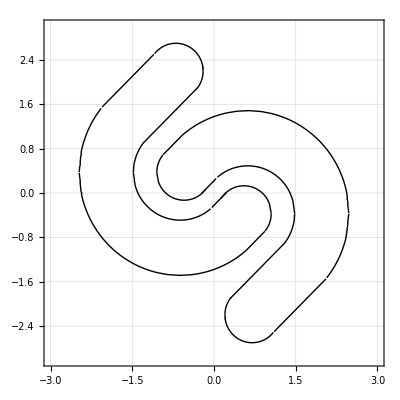

```mathematica
Show[topTipGraph,leftTipGraph,rightTipTopGraph, rightTipRightGraph, bigCircleTopGraph,  bigCircleBottomGraph, smallCircleTopGraph, smallCircleBottomGraph,line1Graph,line2Graph,line3Graph,line4Graph,topTipGraphInv,leftTipGraphInv,rightTipTopGraphInv, rightTipRightGraphInv, bigCircleTopGraphInv,  bigCircleBottomGraphInv, smallCircleTopGraphInv, smallCircleBottomGraphInv,line1GraphInv,line2GraphInv,line3GraphInv,line4GraphInv, PlotRange -> {{-3,3},{-3,3}},GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed]]
```

```mathematica
(topTip-y)*(leftTip-y)*(rightTipTop-y)*(rightTipRight-y)*(bigCircleTop-y)*(bigCircleBottom-y)*(smallCircleTop-y)*(smallCircleBottom-y)*(line1-y)*(line2-y)*(line3-y)*(line4-y)*(topTipInv-y)*(leftTipInv-y)*(rightTipTopInv-y)*(rightTipRightInv-y)*(bigCircleTopInv-y)*(bigCircleBottomInv-y)*(smallCircleTopInv-y)*(smallCircleBottomInv-y)*(line1Inv-y)*(line2Inv-y)*(line3Inv-y)*(line4Inv-y)
```

{{{{{(-y+(0.37-3.71 √(0.5+0.269542 (0.62+x)-(0.5+0.269542 (0.62+x))^2)) (i+(1-i) UnitStep[0.324+0.269542 (-0.62-x)])) (-y+(0.37+1.72 √(0.5-(0.5+0.581395 (0.62-x))^2+0.581395 (0.62-x))) (i+(1-i) UnitStep[-0.39-0.581395 (0.62-x)])) (-y+(0.37-1.72 √(0.5-(0.5+0.581395 (0.62-x))^2+0.581395 (0.62-x))) (i+(1-i) UnitStep[0.324-0.581395 (0.62-x)])) (-y+(0.37+3.71 √(0.5-(0.5+0.269542 (0.62-x))^2+0.269542 (0.62-x))) (i+(1-i) UnitStep[-0.388-0.269542 (0.62-x)])) (-y+(0.37-3.71 √(0.5-(0.5+0.269542 (0.62-x))^2+0.269542 (0.62-x))) (i+(1-i) UnitStep[0.324+0.269542 (-0.62+x)])) (-y+(-0.37-√(-0.05-(-0.05-x)^2-x)) (i+(1-i) UnitStep[-0.94-x])) (-y+(-0.37+√(-0.05-(-0.05-x)^2-x)) (i+(1-i) UnitStep[-0.126-x])) (-y+(2.2-√(1.2-(1.2-x)^2-x)) (i+(1-i) UnitStep[0.31-x])) (-y+(2.2+√(1.2-(1.2-x)^2-x)) (i+(1-i) UnitStep[1.09-x])) (-y+(3.604-x) (i+(1-i) UnitStep[2.054-x]) (i+(1-i) UnitStep[-1.084+x])) (-y+(-0.37-√(-0.05-(-0.05+x)^2+x)) (i+(1-i) UnitStep[-0.94+x])) (-y+(-1.625+x) (i+(1-i) UnitStep[0.935-x]) (i+(1-i) UnitStep[-0.58+x])) (-y+(2.2-x) (i+(1-i) UnitStep[1.3-x]) (i+(1-i) UnitStep[-0.3+x])) (-y+(-0.37+√(-0.05-(-0.05+x)^2+x)) (i+(1-i) UnitStep[-0.126+x])) (-y+(-0.221+x) (i+(1-i) UnitStep[0.241-x]) (i+(1-i) UnitStep[0.059+x])) (-y+(-0.221-x) (i+(1-i) UnitStep[0.059-x]) (i+(1-i) UnitStep[0.241+x])) (-y+(2.2-√(1.2+x-(1.2+x)^2)) (i+(1-i) UnitStep[0.31+x])) (-y+(-1.625-x) (i+(1-i) UnitStep[-0.58-x]) (i+(1-i) UnitStep[0.935+x])) (-y+(2.2+√(1.2+x-(1.2+x)^2)) (i+(1-i) UnitStep[1.09+x])) (-y+(2.2+x) (i+(1-i) UnitStep[-0.3-x]) (i+(1-i) UnitStep[1.3+x])) (-y+(3.604+x) (i+(1-i) UnitStep[-1.084-x]) (i+(1-i) UnitStep[2.054+x])) (-y+(0.37+1.72 √(0.5+0.581395 (0.62+x)-(0.5+0.581395 (0.62+x))^2)) (i+(1-i) UnitStep[-0.39-0.581395 (0.62+x)])) (-y+(0.37-1.72 √(0.5+0.581395 (0.62+x)-(0.5+0.581395 (0.62+x))^2)) (i+(1-i) UnitStep[0.324-0.581395 (0.62+x)])) (-y+(0.37+3.71 √(0.5+0.269542 (0.62+x)-(0.5+0.269542 (0.62+x))^2)) (i+(1-i) UnitStep[-0.388-0.269542 (0.62+x)]))}}}}}

```mathematica
(topTip-y)
```

{{{-y+(2.2+√(1.2+x-(1.2+x)^2)) (i+(1-i) UnitStep[1.09+x])}}}

```mathematica
(topTip-y)
```

{{{-y+(2.2+√(1.2+x-(1.2+x)^2)) (i+(1-i) UnitStep[1.09+x])}}}